```mathematica
values =With[
{p=3, max=3^15},
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [Take[base,- IntegerPart[ Length[base]/2 +1]],p]

], {n, 0,max}]
]
```

{0,1,2,3,4,5,6,7,8,0,1,2,3,4,5,6,7,8,0,1,2,3,4,5,6,7,8,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,«14348754»,6485,6486,6487,6488,6489,6490,6491,6492,6493,6494,6495,6496,6497,6498,6499,6500,6501,6502,6503,6504,6505,6506,6507,6508,6509,6510,6511,6512,6513,6514,6515,6516,6517,6518,6519,6520,6521,6522,6523,6524,6525,6526,6527,6528,6529,6530,6531,6532,6533,6534,6535,6536,6537,6538,6539,6540,6541,6542,6543,6544,6545,6546,6547,6548,6549,6550,6551,6552,6553,6554,6555,6556,6557,6558,6559,6560,0}

```mathematica
Sort[Tally[Sort[values]]]
```

```mathematica
{{0,4},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3}}
Tally[Map[#[[2]]&,Sort[Tally[Sort[values]]]]]
```

{{0,4},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3}}

{{2916,1},{2915,8},{2912,18},{2904,54},{2880,162},{2808,486},{2592,1458},{1944,4374}}

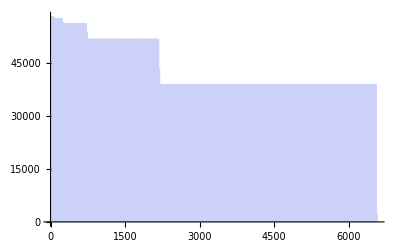

```mathematica
Histogram[values]
```

```mathematica
values2 =With[
{p=3, max=3^10},
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [Reverse[Take[base,-IntegerPart[ Length[base]/2 +1]]],p]

], {n, 0,max}]
]
```

{0,1,2,1,4,7,2,5,8,0,3,6,1,4,7,2,5,8,0,3,6,1,4,7,2,5,8,0,9,18,3,12,21,6,15,24,1,10,19,4,13,22,7,16,25,2,11,20,5,14,23,8,17,26,0,9,18,3,12,21,6,15,24,1,10,19,4,13,22,7,16,25,2,11,20,5,14,23,8,17,26,0,9,18,3,12,21,6,15,24,1,10,19,4,13,22,7,16,25,2,11,20,5,14,23,8,17,26,0,9,18,3,12,21,6,15,24,1,10,19,4,13,22,7,16,25,2,11,20,5,14,23,8,17,26,0,9,18,3,12,21,6,15,24,1,10,19,4,13,«58752»,599,194,437,680,59,302,545,140,383,626,221,464,707,14,257,500,95,338,581,176,419,662,41,284,527,122,365,608,203,446,689,68,311,554,149,392,635,230,473,716,23,266,509,104,347,590,185,428,671,50,293,536,131,374,617,212,455,698,77,320,563,158,401,644,239,482,725,8,251,494,89,332,575,170,413,656,35,278,521,116,359,602,197,440,683,62,305,548,143,386,629,224,467,710,17,260,503,98,341,584,179,422,665,44,287,530,125,368,611,206,449,692,71,314,557,152,395,638,233,476,719,26,269,512,107,350,593,188,431,674,53,296,539,134,377,620,215,458,701,80,323,566,161,404,647,242,485,728,0}

```mathematica
values3 =With[
{p=5, max=3^10},
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [Reverse[Take[base,-IntegerPart[ Length[base]/2 +1]]],p]

], {n, 0,max}]
]
```

{0,1,2,3,4,1,6,11,16,21,2,7,12,17,22,3,8,13,18,23,4,9,14,19,24,0,5,10,15,20,1,6,11,16,21,2,7,12,17,22,3,8,13,18,23,4,9,14,19,24,0,5,10,15,20,1,6,11,16,21,2,7,12,17,22,3,8,13,18,23,4,9,14,19,24,0,5,10,15,20,1,6,11,16,21,2,7,12,17,22,3,8,13,18,23,4,9,14,19,24,0,5,10,15,20,1,6,11,16,21,2,7,12,17,22,3,8,13,18,23,4,9,14,19,24,0,25,50,75,100,5,30,55,80,105,10,35,60,85,110,15,40,65,90,115,20,«58758»,506,31,156,281,406,531,56,181,306,431,556,81,206,331,456,581,106,231,356,481,606,11,136,261,386,511,36,161,286,411,536,61,186,311,436,561,86,211,336,461,586,111,236,361,486,611,16,141,266,391,516,41,166,291,416,541,66,191,316,441,566,91,216,341,466,591,116,241,366,491,616,21,146,271,396,521,46,171,296,421,546,71,196,321,446,571,96,221,346,471,596,121,246,371,496,621,2,127,252,377,502,27,152,277,402,527,52,177,302,427,552,77,202,327,452,577,102,227,352,477,602,7,132,257,382,507,32,157,282,407,532,57,182,307,432,557,82,207,332,457,582,107,232,357,482,607}

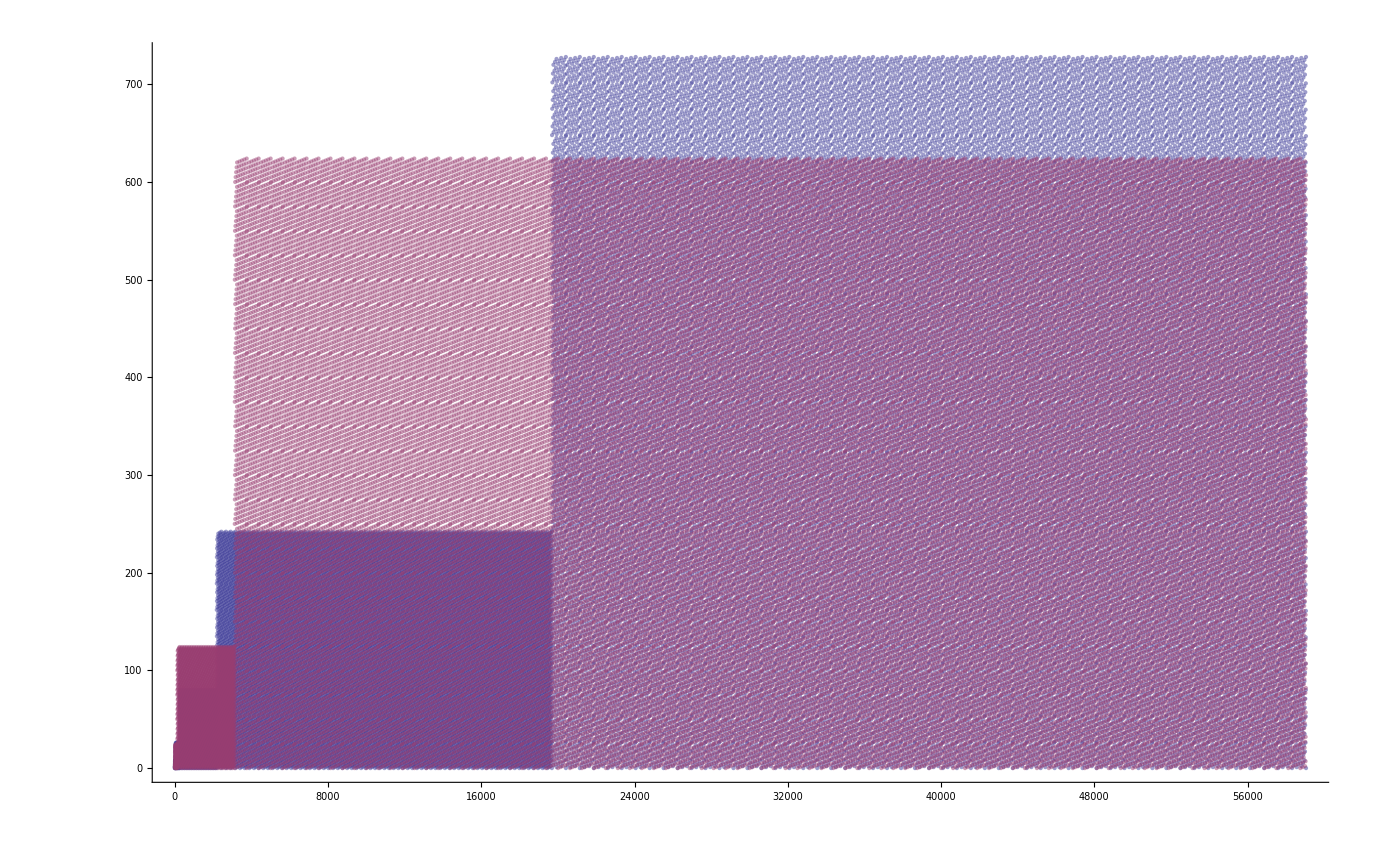

```mathematica
ListPlot[{values2, values3}, PlotStyle->Opacity[0.5]]
```

```mathematica
values3 =With[
{p=5, max=3^15},
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [{Last[Take[base,IntegerPart[ Length[base]/2 +1]]]},p]

], {n, 0,max}]
]
```

$Aborted

```mathematica
Tally[
With[
{p=5, max=3^10},
Tally[
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [{Last[Take[base,IntegerPart[ Length[base]/2 +1]]]},p]

], {n, 0,max}]
]
]
]
```

{{{0,11875},1},{{1,11875},1},{{2,11800},1},{{3,11750},1},{{4,11750},1}}

```mathematica
MiddleDigit[p_,n_] :=With[
{base = IntegerDigits[n,p]},
FromDigits [{Last[Take[base,IntegerPart[ Length[base]/2 +1]]]},p]

]
```

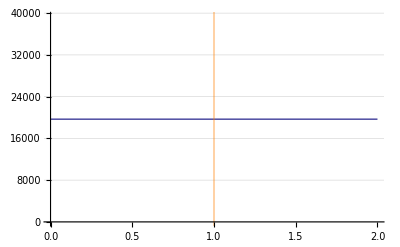

```mathematica
With[
{p=3, max=3^10},
ListLinePlot[
Tally[
Table[
With[
{base = IntegerDigits[n,p]},
FromDigits [{Last[Take[base,IntegerPart[ Length[base]/2 +1]]]},p]

], {n, 0,max-1}]
],
GridLines->{{{1, Directive[Orange,Thick]}}, Automatic}

]
]
```

```mathematica
MiddleDigit[p_,n_] :=With[
{base = IntegerDigits[n,p]},
Take[base,IntegerPart[ Length[base]/2 +1]]

]
```

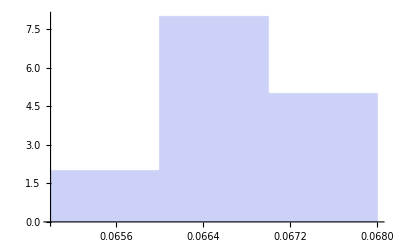

```mathematica
Histogram[
Sort[
With[
{p=3,q=5,max=(3*5)^4},
Map[
N[Norm[{(p*q)/max, #[[2]]/max}]]&,
Tally[Table[{MiddleDigit[p,i],MiddleDigit[q,i]},{i,0,max}]]
]
]
]
]
```

```mathematica
With[
{p=3,q=5,max=300},
Map[
Norm[{p*q/max, #[[2]]/max}]&,
Tally[Table[{MiddleDigit[p,i],MiddleDigit[q,i]},{i,0,max}]]
]
]
```

```mathematica
q=With[
{p=3,q=5,max=(3*5)^6},
Map[
N[Norm[{(p*q)/max, #[[2]]/max}]]&,
Tally[Table[{MiddleDigit[p,i],MiddleDigit[q,i]},{i,0,max}]]
]
]
```

{0.0667088,0.0666126,0.0668675,0.0667245,0.0667654,0.0666337,0.0667969,0.0666041,0.0666031,0.0666174,0.0666724,0.0665905,0.0666172,0.0665284,0.0666575}

```mathematica
N[1/15]
```

0.0666667

```mathematica
Skewness[N[q]]
```

0.75606

```mathematica
Kurtosis[N[q]]
```

2.85579

```mathematica
Norm[2]
```

2

```mathematica
AllSame[tallyList_] := Module[{index, s=Mean[Table[l[[2]],{l, tallyList}]]},
For[index=1, index≤ Length[tallyList], index++,
If[tallyList[[index]][[2]] ≠ s,
Return[False]
]
];
Return[True]
]
```

```mathematica
AllSame[{{2,3},{3,2}}]
```

5/2

False

```mathematica
Module[{max, abs=1000000},
With[
{p=3,q=5},
With[
{lots = Table[{MiddleDigit[p,i],MiddleDigit[q,i]},{i,0,abs}]},
Monitor[
For[max=0,max<abs,max+=p*q,
With[
{l = Tally[Take[lots,max]]},
If[AllSame[l],
Print[{max,l}]
];
]
],
max
]
]
]
]
```

{0,{}}

```mathematica
Middle[tuple_]:= tuple[[IntegerPart[(Length[tuple]+1)/2]]]
```

```mathematica
AllEqual[m_] := Module[{i,j, level},
level= m[[1]][[1]];
For[i=1,i< Length[m], i++,
For[j=1,j< Length[m[[i]]], j++,
If[m[[i]][[j]] ≠ level, Return[False]]
]
];
Return[True];
]
```

```mathematica
MyMatrixMiddle[p_,q_,max_] := Module[
{ current, result, digitp, digitq},
result = Array[0&,{p,q}];
Monitor[
For[current=0, current < max, current++,

digitp = Middle[IntegerDigits[current,p]]+1;
digitq = Middle[IntegerDigits[current,q]]+1;
result[[digitp, digitq]] =result[[digitp, digitq]] + 1;

],
ToString[current] <> "/" <> ToString[max]
];
Return [result];
]
```

```mathematica
With[
{p=3,q=5, max=10000},
Animate[
ListPlot3D[
MapAll[#/(n+1)&,MyMatrixLast[p,q,n]],
PlotLabel->n,
ColorFunction->"DarkRainbow"
]
,{n,10000,max,1},
AnimationRunning->False,
DisplayAllSteps->True
]
]
```

```mathematica
MyMatrixMiddle[3,5,1000000000]
```

{0,{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

$Aborted

```mathematica
AllEqual[{{1,1},{1,1},{1,1}}]
```

True

```mathematica
MyMatrixFirst[p_,q_,max_] := Module[
{ current, result, digitp, digitq},
result = Array[0&,{p,q}];
Monitor[
For[current=0, current < max, current++,
If[Mod[current,p*q]==0,
If[AllEqual[result],
Print[{current, result}]
]
];
digitp = First[IntegerDigits[current,p]]+1;
digitq = First[IntegerDigits[current,q]]+1;
result[[digitp, digitq]] =result[[digitp, digitq]] + 1;

],
ToString[current] <> "/" <> ToString[max]
];
Return [result];
]
```

```mathematica
MyMatrixFirst[3,5,1000000]
```

{0,{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

{{1,0,0,0,0},{0,303189,287250,85148,58692},{0,185092,29156,12508,38964}}

```mathematica
MyMatrixLast[p_,q_,max_] := Module[
{ current, result, digitp, digitq},
result = Array[0&,{p,q}];
Monitor[
For[current=0, current < max, current++,
If[Mod[current,p*q]==0,
If[AllEqual[result],
Print[{current, result}]
]
];
digitp = Last[IntegerDigits[current,p]]+1;
digitq = Last[IntegerDigits[current,q]]+1;
result[[digitp, digitq]] =result[[digitp, digitq]] + 1;

],
ToString[current] <> "/" <> ToString[max]
];
Return [result];
]
```

```mathematica
MyMatrixLast[3,5,1000]
```

{{67,67,66,67,67},{66,67,67,66,67},{67,66,67,67,66}}

```mathematica
AllEqual[{{61,61,61,61,61},{61,61,61,61,61},{61,61,61,61,61}}]
```

True

```mathematica
AllEqual[m_] := Module[{i,j, level},
level= m[[1]][[1]];
For[i=1,i< Length[m], i++,
For[j=1,j< Length[m[[i]]], j++,
If[m[[i]][[j]] ≠ level, Return[{i,j}]]
]
];
Return[True];
]
```

```mathematica
With[
{p=5,q=2, max=100000},
Animate[
BarChart[
Ratios [MyMatrixMiddle[p,q,n]],
PlotLabel->n,
ColorFunction->"DarkRainbow"
]
,{n,0,max,100},
AnimationRunning->False,
DisplayAllSteps->True
]
]
```

```mathematica
MyMatrixMiddle[2,3,100]
```

{0,{{0,0,0},{0,0,0}}}

```mathematica
{{{20,17,14},{14,20,15}}}
```

{0,{{0,0,0},{0,0,0}}}

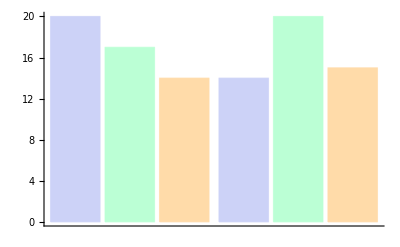

```mathematica
BarChart[MyMatrixMiddle[2,3,100]]
```

```mathematica
With[
{p=3,q=5, max=2000},
MyMatrixLast[p,q,max]
]
```

{{134,133,133,134,133},{133,134,133,133,134},{133,133,134,133,133}}

```mathematica
MapAll[Sum[p,{p,#}]&, {{1348,1270,1363,1463,1358},{1306,1389,1351,1266,1324},{1342,1342,1287,1272,1319}}]
```

13362119

```mathematica
N[2/15]
```

0.133333

```mathematica
1348*15
```

20220

```mathematica
MiddleDigit[p_,n_] :=With[
{base = Reverse[IntegerDigits[n,p]]},
base[[IntegerPart[ Floor[(Length[base]+1)/2 ]]]]

]
```

```mathematica
MiddleDigitTable[p_,max_] := Module[
{runLength, countRuns, height, result, current, currentRun, currentDigit, currentInRun},
current=1;(* we have to start at 1 for the algorithm to work - 0 is causing troubles *)
currentDigit := 1; (* because we start at 1, the first digit is 1 *) 
countRuns=p*p-1; (* because of the start at 1, we need one less run to start with *)
runLength=1; (* we start by alternating digits of length 1 *)
height=1; (* if you'r interested : the height of the current digit (from the right *)
result=Range[max];
While[current≤ max,
For[currentRun = 1 , currentRun ≤ countRuns, currentRun ++,
For[currentInRun = 1 , currentInRun ≤ runLength, currentInRun ++,
If[current > max, Return[result]];
result[[current]] =  currentDigit;
current +=1;
];
currentDigit = Mod[currentDigit+1,p];
];
runLength *=p; (* runlengths grow expoentially *)
countRuns *=p; (* number of runs grows exponentially *)
height +=1; (* height is the log so just increments *)
];
Return[result];
]
```

```mathematica
Map[{First[#], Length[#]}&,SplitBy[Table[MiddleDigit[2,i],{i,0,100}],#&]]
```

{{0,1},{1,1},{0,1},{1,1},{0,2},{1,2},{0,2},{1,2},{0,2},{1,2},{0,4},{1,4},{0,4},{1,4},{0,4},{1,4},{0,4},{1,4},{0,4},{1,4},{0,4},{1,4},{0,8},{1,8},{0,8},{1,8},{0,5}}

```mathematica
CountRunLength[table_] := Map[{First[#][[2]],Length[#]}&,SplitBy[table,#[[2]]&]]
```

```mathematica
CountRunLength[CountRunLength[MyTable[3,20000]]]
```

{{1,9},{3,36},{9,144},{27,576},{81,37},{39,1}}

```mathematica
Map[#[[2]]&,CountRunLength[CountRunLength[Table[{i,MiddleDigit[3,i]},{i,0,3^12-1}]]]]
```

{9,24,72,216,648,1944}

```mathematica
SplitBy[Map[{First[#][[2]],Length[#]}&,SplitBy[MyTable[3,10000],#[[2]]&]],#[[2]]&]
```

```mathematica
Map[{First[#][[2]],Length[#]}&,SplitBy[Map[{First[#][[2]],Length[#]}&,SplitBy[MyTable[3,10000],#[[2]]&]],#[[2]]&]]
```

{{1,9},{3,27},{9,81},{27,243},{81,32},{28,1}}

```mathematica
Table[{i,MiddleDigit[3,i]},{i,0,20000}]
```

{{0,0},{1,1},{2,2},{3,0},{4,1},{5,2},{6,0},{7,1},{8,2},{9,0},{10,0},{11,0},{12,1},{13,1},{14,1},{15,2},{16,2},{17,2},{18,0},{19,0},{20,0},{21,1},{22,1},{23,1},{24,2},{25,2},{26,2},{27,0},{28,0},{29,0},{30,1},{31,1},{32,1},{33,2},{34,2},{35,2},{36,0},{37,0},{38,0},{39,1},{40,1},{41,1},{42,2},{43,2},{44,2},{45,0},{46,0},{47,0},{48,1},{49,1},{50,1},{51,2},{52,2},{53,2},{54,0},{55,0},«19889»,{19945,0},{19946,0},{19947,0},{19948,0},{19949,0},{19950,0},{19951,0},{19952,0},{19953,0},{19954,0},{19955,0},{19956,0},{19957,0},{19958,0},{19959,0},{19960,0},{19961,0},{19962,0},{19963,0},{19964,0},{19965,0},{19966,0},{19967,0},{19968,0},{19969,0},{19970,0},{19971,0},{19972,0},{19973,0},{19974,0},{19975,0},{19976,0},{19977,0},{19978,0},{19979,0},{19980,0},{19981,0},{19982,0},{19983,0},{19984,0},{19985,0},{19986,0},{19987,0},{19988,0},{19989,0},{19990,0},{19991,0},{19992,0},{19993,0},{19994,0},{19995,0},{19996,0},{19997,0},{19998,0},{19999,0},{20000,0}}

```mathematica
3^(2*3)
```

729

```mathematica
Module[
{i},f
With[
{a=Table[{i,MiddleDigit[3,i]},{i,1,3^10-1}],
b=MyTable[3,3^10-1]},
For[i=1,i≤Length[a],i++,
If[a[[i]]≠b[[i]],
Print[{a[[i]],b[[i]]}];
Return[];
]
]
]
]
```

At 9 runlength becomes 3

At 9 countruns becomes 24

At 81 runlength becomes 9

At 81 countruns becomes 72

At 729 runlength becomes 27

At 729 countruns becomes 216

At 6561 runlength becomes 81

At 6561 countruns becomes 648

At 59049 runlength becomes 243

At 59049 countruns becomes 1944

```mathematica
Table[{i,MiddleDigit[3,i]},{i,1,20000}]
```

{{1,1},{2,2},{3,0},{4,1},{5,2},{6,0},{7,1},{8,2},{9,0},{10,0},{11,0},{12,1},{13,1},{14,1},{15,2},{16,2},{17,2},{18,0},{19,0},{20,0},{21,1},{22,1},{23,1},{24,2},{25,2},{26,2},{27,0},{28,0},{29,0},{30,1},{31,1},{32,1},{33,2},{34,2},{35,2},{36,0},{37,0},{38,0},{39,1},{40,1},{41,1},{42,2},{43,2},{44,2},{45,0},{46,0},{47,0},{48,1},{49,1},{50,1},{51,2},{52,2},{53,2},{54,0},{55,0},{56,0},«19888»,{19945,0},{19946,0},{19947,0},{19948,0},{19949,0},{19950,0},{19951,0},{19952,0},{19953,0},{19954,0},{19955,0},{19956,0},{19957,0},{19958,0},{19959,0},{19960,0},{19961,0},{19962,0},{19963,0},{19964,0},{19965,0},{19966,0},{19967,0},{19968,0},{19969,0},{19970,0},{19971,0},{19972,0},{19973,0},{19974,0},{19975,0},{19976,0},{19977,0},{19978,0},{19979,0},{19980,0},{19981,0},{19982,0},{19983,0},{19984,0},{19985,0},{19986,0},{19987,0},{19988,0},{19989,0},{19990,0},{19991,0},{19992,0},{19993,0},{19994,0},{19995,0},{19996,0},{19997,0},{19998,0},{19999,0},{20000,0}}

```mathematica
MyTable[3,20000]
```

At 9 runlength becomes 3

At 9 countruns becomes 24

At 81 runlength becomes 9

At 81 countruns becomes 72

At 729 runlength becomes 27

At 729 countruns becomes 216

At 6561 runlength becomes 81

At 6561 countruns becomes 648

{{1,1},{2,2},{3,0},{4,1},{5,2},{6,0},{7,1},{8,2},{9,0},{10,0},{11,0},{12,1},{13,1},{14,1},{15,2},{16,2},{17,2},{18,0},{19,0},{20,0},{21,1},{22,1},{23,1},{24,2},{25,2},{26,2},{27,0},{28,0},{29,0},{30,1},{31,1},{32,1},{33,2},{34,2},{35,2},{36,0},{37,0},{38,0},{39,1},{40,1},{41,1},{42,2},{43,2},{44,2},{45,0},{46,0},{47,0},{48,1},{49,1},{50,1},{51,2},{52,2},{53,2},{54,0},{55,0},{56,0},«19888»,{19945,0},{19946,0},{19947,0},{19948,0},{19949,0},{19950,0},{19951,0},{19952,0},{19953,0},{19954,0},{19955,0},{19956,0},{19957,0},{19958,0},{19959,0},{19960,0},{19961,0},{19962,0},{19963,0},{19964,0},{19965,0},{19966,0},{19967,0},{19968,0},{19969,0},{19970,0},{19971,0},{19972,0},{19973,0},{19974,0},{19975,0},{19976,0},{19977,0},{19978,0},{19979,0},{19980,0},{19981,0},{19982,0},{19983,0},{19984,0},{19985,0},{19986,0},{19987,0},{19988,0},{19989,0},{19990,0},{19991,0},{19992,0},{19993,0},{19994,0},{19995,0},{19996,0},{19997,0},{19998,0},{19999,0},{20000,0}}

```mathematica
With[
{p=2,q=5, max=100000},
Histogram[
Table[
{Middle[IntegerDigits[n,p]] , Middle[IntegerDigits[n,q]]}
,{n,1,max}
]
]
]
```

$Aborted

```mathematica
Timing[With[
{l = MiddleDigitTable[3,10000000]},
{N[Kurtosis[l]],
N[Skewness[l]],
N[StandardDeviation[l]]
}
]
]
```

{378.568,{1.49992,0.00019033,0.816518}}

```mathematica
N[Kurtosis[{0,1,2,3,4,5,6,7,8,9,10}]]
```

1.78

```mathematica
Timing[With[
{l = MiddleDigitTable[3,3^16]},
{N[Kurtosis[l]],
N[Skewness[l]],
N[StandardDeviation[l]]
}
]
]
```

{362.562,{1.5,0.,0.816497}}

```mathematica
Rationalize[0.81649]
```

81649/100000

```mathematica
N[StandardDeviation[{0,1,2}]]
```

1.

```mathematica
N[Log[3,10000000]]
```

14.6713

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

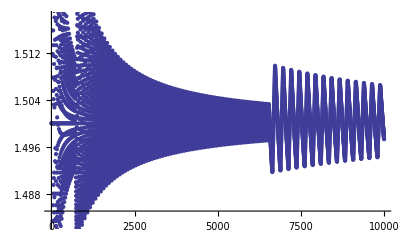

```mathematica
With[
{digits=MiddleDigitTable[3,10000]},
ListPlot[Table[{n,Kurtosis[Take[digits,n]]},{n,1,10000}]]
]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

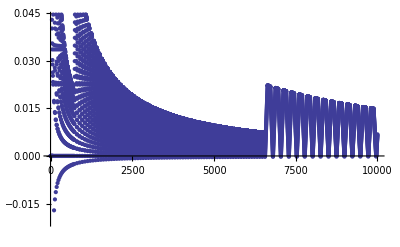

```mathematica
With[
{digits=MiddleDigitTable[3,10000]},
ListPlot[Table[{n,Skewness[Take[digits,n]]},{n,1,10000}]]
]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

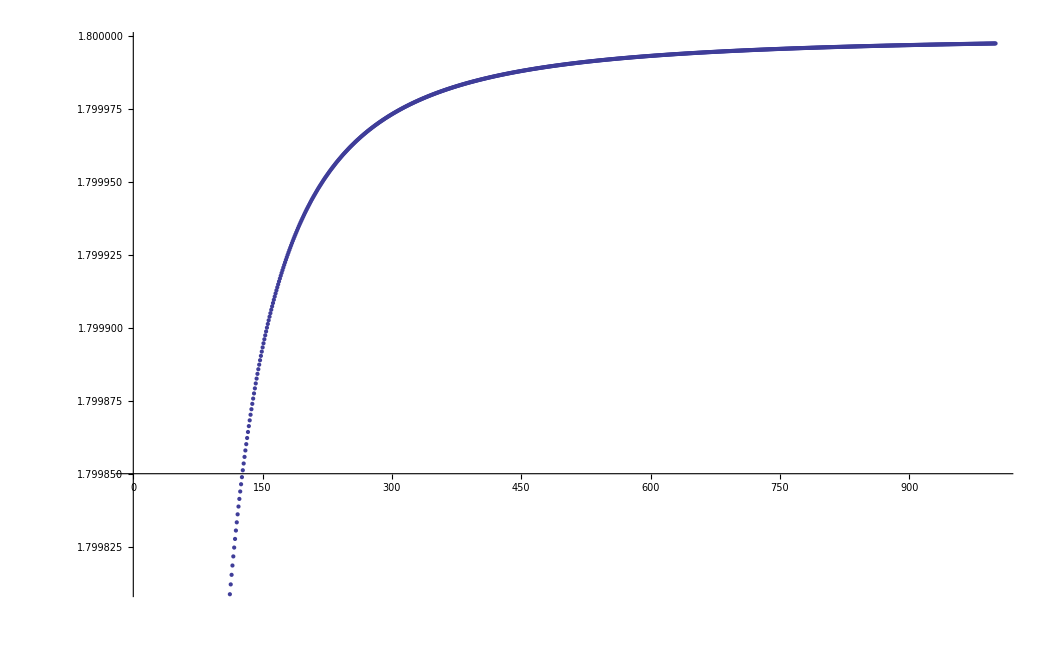

```mathematica
ListPlot[Table[{n,Kurtosis[Range[n]]},{n,1,1000}]]
```

```mathematica
Limit[Kurtosis[Range[n]],n->Infinity]
```

Range::range: Range specification in Range[n] does not have appropriate bounds.

Kurtosis::vecmat1: Argument Range[n] is neither a non-empty vector nor a non-empty matrix.

Limit[Kurtosis[Range[n]],n→∞]

```mathematica
N[Log[3,2000000]]
```

13.2063

```mathematica
3^16
```

43046721

```mathematica
Kurtosis[{a,b}]
```

(2 ((a+1/2 (-a-b))^4+(1/2 (-a-b)+b)^4))/(((a+1/2 (-a-b))^2+(1/2 (-a-b)+b)^2)^2)

```mathematica
N[Limit[Kurtosis[{a,b,c,d,e}], a->Infinity]]
```

3.25

```mathematica
18911429680*2
```

37822859360

```mathematica
l = {{1,2},{2,11},{3,22},{4,51},{5,63},{6,75},{7,90},{9,98},{10,105},{12,140},{15,161},{16,203},{18,210},{22,756},{25,861},{26,999},{29,1106},{30,1350},{36,2430},{46,2538},{47,2835},{56,2862},{59,2970},{62,3159},{65,4536},{66,6713},{74,7350},{78,7938},{84,7987},{89,10339},{91,16170},{92,22001},{93,27832},{94,33663},{96,59388},{112,59829},{126,59878},{145,60074},{175,60564},{191,61103},{205,61789},{211,67620},{217,73451},{223,79282},{229,85113},{235,90944},{241,96775},{247,102606},{253,108437},{258,114268},{307,117855},{314,118335},{337,118584},{459,120285},{481,121257},{483,154791},{738,531993},{992,534357},{1051,535766},{1084,536544},{1229,538002},{1324,539460},{1348,540911},{1374,541647},{1484,543105},{1491,763992},{1492,2996919},{1493,4002939},{1575,4787937},{1596,4833556},{1716,4859967},{1730,5325761},{1731,5424202},{3440,5767119},{3766,5799924},{3786,6068925},{3787,8522739},{3794,9749646},{3805,10976553},{3820,12203460},{3839,13430367},{3862,14657274},{3888,15884181},{3910,17111088},{3928,18337995},{3940,19564902},{3944,20791809},{4210,43052331},{5066,43061935},{6611,43069138},{7083,43095549},{7214,43304436},{7446,43422085},{7472,45724644},{7474,229189856},{7476,256450810},{13033,282483855},{14031,282601953},{16458,282720051},{18885,282838149},{21564,282956247},{24440,283074345},{27316,283192443},{30192,283310541},{33068,283428639},{35610,283546737},{37703,283664835},{39347,283782933},{40745,283901031},{42445,284019129},{45321,284137227},{48045,284255325},{50320,284373423},{52146,284491521},{53523,284609619},{54121,284727387},{54200,300257055},{54209,305433611},{54229,336375298},{54250,367316985},{59553,387569420},{59722,387636648},{61675,387653455},{70254,387687069},{71417,387735417},{76529,387754297},{77679,387771104},{80506,387804718},{86600,387853515},{93336,387871946},{102232,387971613},{110143,387989595},{118313,388089711},{126950,388107244},{134843,388207809},{143757,388224893},{151650,388325735},{160392,388342542},{168457,388443384},{176578,388460191},{185264,388561033},{192315,388577840},{202071,388678682},{207603,388695489},{218878,388796331},{222442,388813138},{235685,388913980},{236832,388930787},{252492,389031629},{268860,389149278},{284779,389266927},{300249,389384576},{315270,389502225},{329842,389619874},{343965,389737523},{357382,389855172},{358534,389956014},{369901,389972821},{373031,390073663},{381522,390090470},{387485,390191312},{393100,390208119},{402239,390308961},{404978,390325768},{416544,390426610},{430400,390544259},{443807,390661908},{456765,390779557},{469274,390897206},{481334,391014855},{492945,391132504},{504107,391250153},{514478,391367802},{523951,391485451},{533327,391603100},{542693,391720749},{551610,391838398},{560078,391956047},{568097,392073696},{575667,392191345},{576351,392292187},{582788,392308994},{585899,392409836},{589460,392426643},{594998,392527485},{595683,392544292},{595924,392628327},{603648,392645134},{607001,392745976},{611849,392762783},{617202,392863625},{619174,392880432},{626505,392981274},{634910,393098923},{642417,393216572},{649026,393334221},{654737,393451870},{659550,393569519},{665608,393687168},{672644,393804817},{679231,393922466},{685369,394040115},{691058,394157764},{696235,394275413},{700514,394393062},{703895,394510711},{706378,394628360},{707963,394746009},{708650,394863658},{708655,534160074},{708671,565101761},{708695,596043448},{708717,626985135},{708728,657926822},{720375,31384956843},{722083,31386551166},{750370,31393991340},{755479,31410466011},{756777,31426940682},{756876,31999302639},{756889,34985469618},{756912,43139368881},{756914,64614899691},{756916,86090430501},{756918,107565961311},{756919,129041492121},{821823,282431365923},{882847,282433013009},{891108,282434660095},{967017,282437954267},{1084666,282439601353},{1182059,282441228183},{1206433,282442822506},{1217866,282492246519},{1219067,282616603713},{1219639,283188965670},{1219699,286175132649},{1247570,678227129964},{1254320,678333418164},{1260117,678408351345},{1280627,678691609398},{1286372,678766542579},{1286778,699669711432},{1287324,702655878411},{1287984,705642045390},{1288705,708628212369},{1289487,711614379348},{1290330,714600546327},{1291234,717586713306},{1292199,720572880285},{1293225,723559047264},{1294305,726545214243},{1295385,729531381222},{1296465,732517548201},{1297545,735503715180},{1298625,738489882159},{1299611,741476049138},{1300475,744462216117},{1301217,747448383096},{1301837,750434550075},{1302335,753420717054},{1302711,756406884033},{1302965,759393051012},{1303097,762379217991},{1303107,765365384970},{1303114,915694100640},{1832538,2541872057844},{2134573,2541880177236},{2135494,2541908875050},{2214653,2541958299063},{2227007,2541986996877},{2236239,2542407898149},{2236304,2543503198050},{2239487,2545468998309},{2242292,2547434798568},{2242353,2688805013301},{2242355,5253351680628},{2242356,9170856788985}}
```

{{1,2},{2,11},{3,22},{4,51},{5,63},{6,75},{7,90},{9,98},{10,105},{12,140},{15,161},{16,203},{18,210},{22,756},{25,861},{26,999},{29,1106},{30,1350},{36,2430},{46,2538},{47,2835},{56,2862},{59,2970},{62,3159},{65,4536},{66,6713},{74,7350},{78,7938},{84,7987},{89,10339},{91,16170},{92,22001},{93,27832},{94,33663},{96,59388},{112,59829},{126,59878},{145,60074},{175,60564},{191,61103},{205,61789},{211,67620},{217,73451},{223,79282},{229,85113},{235,90944},{241,96775},{247,102606},{253,108437},{258,114268},{307,117855},{314,118335},{337,118584},{459,120285},{481,121257},{483,154791},{738,531993},{992,534357},{1051,535766},{1084,536544},{1229,538002},{1324,539460},{1348,540911},{1374,541647},{1484,543105},{1491,763992},{1492,2996919},{1493,4002939},{1575,4787937},{1596,4833556},{1716,4859967},{1730,5325761},{1731,5424202},{3440,5767119},{3766,5799924},{3786,6068925},{3787,8522739},{3794,9749646},{3805,10976553},{3820,12203460},{3839,13430367},{3862,14657274},{3888,15884181},{3910,17111088},{3928,18337995},{3940,19564902},{3944,20791809},{4210,43052331},{5066,43061935},{6611,43069138},{7083,43095549},{7214,43304436},{7446,43422085},{7472,45724644},{7474,229189856},{7476,256450810},{13033,282483855},{14031,282601953},{16458,282720051},{18885,282838149},{21564,282956247},{24440,283074345},{27316,283192443},{30192,283310541},{33068,283428639},{35610,283546737},{37703,283664835},{39347,283782933},{40745,283901031},{42445,284019129},{45321,284137227},{48045,284255325},{50320,284373423},{52146,284491521},{53523,284609619},{54121,284727387},{54200,300257055},{54209,305433611},{54229,336375298},{54250,367316985},{59553,387569420},{59722,387636648},{61675,387653455},{70254,387687069},{71417,387735417},{76529,387754297},{77679,387771104},{80506,387804718},{86600,387853515},{93336,387871946},{102232,387971613},{110143,387989595},{118313,388089711},{126950,388107244},{134843,388207809},{143757,388224893},{151650,388325735},{160392,388342542},{168457,388443384},{176578,388460191},{185264,388561033},{192315,388577840},{202071,388678682},{207603,388695489},{218878,388796331},{222442,388813138},{235685,388913980},{236832,388930787},{252492,389031629},{268860,389149278},{284779,389266927},{300249,389384576},{315270,389502225},{329842,389619874},{343965,389737523},{357382,389855172},{358534,389956014},{369901,389972821},{373031,390073663},{381522,390090470},{387485,390191312},{393100,390208119},{402239,390308961},{404978,390325768},{416544,390426610},{430400,390544259},{443807,390661908},{456765,390779557},{469274,390897206},{481334,391014855},{492945,391132504},{504107,391250153},{514478,391367802},{523951,391485451},{533327,391603100},{542693,391720749},{551610,391838398},{560078,391956047},{568097,392073696},{575667,392191345},{576351,392292187},{582788,392308994},{585899,392409836},{589460,392426643},{594998,392527485},{595683,392544292},{595924,392628327},{603648,392645134},{607001,392745976},{611849,392762783},{617202,392863625},{619174,392880432},{626505,392981274},{634910,393098923},{642417,393216572},{649026,393334221},{654737,393451870},{659550,393569519},{665608,393687168},{672644,393804817},{679231,393922466},{685369,394040115},{691058,394157764},{696235,394275413},{700514,394393062},{703895,394510711},{706378,394628360},{707963,394746009},{708650,394863658},{708655,534160074},{708671,565101761},{708695,596043448},{708717,626985135},{708728,657926822},{720375,31384956843},{722083,31386551166},{750370,31393991340},{755479,31410466011},{756777,31426940682},{756876,31999302639},{756889,34985469618},{756912,43139368881},{756914,64614899691},{756916,86090430501},{756918,107565961311},{756919,129041492121},{821823,282431365923},{882847,282433013009},{891108,282434660095},{967017,282437954267},{1084666,282439601353},{1182059,282441228183},{1206433,282442822506},{1217866,282492246519},{1219067,282616603713},{1219639,283188965670},{1219699,286175132649},{1247570,678227129964},{1254320,678333418164},{1260117,678408351345},{1280627,678691609398},{1286372,678766542579},{1286778,699669711432},{1287324,702655878411},{1287984,705642045390},{1288705,708628212369},{1289487,711614379348},{1290330,714600546327},{1291234,717586713306},{1292199,720572880285},{1293225,723559047264},{1294305,726545214243},{1295385,729531381222},{1296465,732517548201},{1297545,735503715180},{1298625,738489882159},{1299611,741476049138},{1300475,744462216117},{1301217,747448383096},{1301837,750434550075},{1302335,753420717054},{1302711,756406884033},{1302965,759393051012},{1303097,762379217991},{1303107,765365384970},{1303114,915694100640},{1832538,2541872057844},{2134573,2541880177236},{2135494,2541908875050},{2214653,2541958299063},{2227007,2541986996877},{2236239,2542407898149},{2236304,2543503198050},{2239487,2545468998309},{2242292,2547434798568},{2242353,2688805013301},{2242355,5253351680628},{2242356,9170856788985}}

```mathematica
TableForm[Map[{IntegerDigits[#[[2]],3],IntegerDigits[#[[1]],7]}&,l],TableDepth->2]
```

{2} | {1}
{1,1,0} | {2}
{2,1,2} | {3}
{1,0,0,0} | {4}
{1,0,1,0} | {5}
{2,0,0,0} | {6}
{2,0,2,0} | {1,0}
{1,0,1,1,2} | {1,2}
{1,0,2,2,0} | {1,4}
{1,1,0,2,1} | {1,5}
{1,1,2,1,1} | {2,0}
{1,2,0,1,2} | {2,2}
{2,0,0,1,0} | {2,5}
{2,1,0,0,1} | {2,6}
{2,1,2,1,0} | {3,0}
{2,2,2,0,1} | {3,1}
{1,0,1,0,1,2} | {3,2}
{1,0,1,2,0,2} | {3,3}
{2,1,2,2,0,0} | {4,3}
{1,0,0,0,2,1,0} | {5,6}
{1,0,0,1,2,0,1} | {6,4}
{1,1,0,1,0,0,0} | {1,0,5}
{1,1,0,1,2,2,2} | {1,1,4}
{1,2,0,2,0,0,0} | {1,1,5}
{1,0,1,2,2,0,0,0} | {1,1,6}
{1,0,0,0,0,2,1,0,1} | {1,2,0}
{1,0,0,1,0,1,2,0,1} | {1,2,5}
{1,0,0,1,0,2,1,2,2} | {1,4,4}
{1,0,0,2,0,1,2,2,2} | {1,5,6}
{1,0,0,2,0,2,2,2,0} | {2,0,5}
{1,0,1,0,0,2,0,2,0} | {2,1,6}
{1,0,1,0,1,0,0,0,0} | {2,3,1}
{1,0,1,1,0,2,1,1,1} | {2,4,6}
{1,0,1,2,0,2,2,0,2} | {2,6,6}
{1,0,2,0,1,0,0,0,0} | {3,0,6}
{1,0,2,0,1,2,2,1,0} | {3,1,1}
{1,0,2,1,1,0,0,0,0} | {3,1,2}
{1,0,2,1,2,0,0,0,0} | {3,2,5}
{1,1,0,0,0,2,2,1,2} | {3,3,3}
{1,1,0,1,1,0,0,0,0} | {3,3,4}
{1,1,2,1,2,2,0,0,0,0} | {3,4,4}
{1,2,1,1,2,2,0,0,0,0} | {3,6,1}
{2,0,0,1,2,2,0,0,0,0} | {4,0,5}
{2,0,2,1,2,2,0,0,0,0} | {4,2,1}
{2,1,1,1,2,2,0,0,0,0} | {4,3,3}
{2,2,0,1,2,2,0,0,0,0} | {4,4,4}
{2,2,2,1,2,2,0,0,0,0} | {4,5,3}
{1,0,0,0,0,0,2,1,1,1,0} | {6,0,6}
{1,0,0,0,1,0,1,0,1,2,1} | {1,0,3,5}
{1,0,0,0,1,1,1,0,2,1,2} | {1,0,4,1}
{1,0,1,2,0,1,0,0,2,1,2} | {1,0,6,3}
{1,0,2,1,0,1,0,0,2,2,0} | {1,1,2,3}
{1,1,0,0,0,1,0,0,2,2,1} | {1,1,5,3}
{1,1,0,2,0,1,0,0,2,2,2} | {1,2,1,3}
{1,1,1,1,0,1,0,1,0,0,0} | {1,2,4,3}
{1,1,2,0,0,1,0,1,0,0,1} | {1,3,0,3}
{1,1,2,2,0,1,0,1,0,0,2} | {1,3,3,3}
{1,2,0,1,0,1,0,1,0,1,0} | {1,3,6,3}
{1,2,1,0,0,1,0,1,0,1,1} | {1,4,2,3}
{1,2,1,2,0,1,0,1,0,1,2} | {1,4,5,3}
{1,2,2,1,0,1,0,1,0,2,0} | {1,5,1,3}
{2,0,0,0,0,1,0,1,0,2,1} | {1,5,4,3}
{2,0,0,2,0,1,0,1,0,2,2} | {1,6,0,3}
{2,0,1,1,0,1,0,1,1,0,0} | {1,6,3,2}
{2,0,2,0,0,1,0,1,1,0,1} | {1,6,6,0}
{2,0,2,2,0,1,0,1,1,0,2} | {2,0,1,4}
{2,1,0,1,0,1,0,1,1,1,0} | {2,0,4,0}
{2,1,1,0,0,0,0,1,0,2,0} | {2,0,4,2}
{2,1,1,0,0,1,0,1,1,1,1} | {2,0,6,2}
{2,1,1,2,0,0,0,1,0,2,1} | {2,1,0,2}
{2,1,1,2,0,1,0,1,1,1,2} | {2,1,1,3}
{2,1,2,1,0,0,0,1,0,2,2} | {2,1,3,2}
{2,1,2,1,0,1,0,1,1,2,0} | {2,1,3,3}
{2,2,0,0,0,0,0,1,1,0,0} | {2,1,6,1}
{2,2,0,2,0,0,0,1,1,0,1} | {2,2,1,6}
{2,2,1,1,0,0,0,1,1,0,2} | {2,2,4,3}
{2,2,2,0,0,0,0,1,1,1,0} | {2,2,6,6}
{2,2,2,2,0,0,0,1,1,1,1} | {2,3,2,1}
{1,0,0,0,1,0,0,0,1,1,1,2} | {2,3,4,2}
{1,0,0,1,0,0,0,0,1,1,2,0} | {2,3,6,2}
{1,0,0,1,2,0,0,0,1,1,2,1} | {2,4,1,1}
{1,0,0,2,1,0,0,0,1,1,2,2} | {2,4,2,6}
{1,0,1,0,0,0,0,0,1,2,0,0} | {2,4,4,3}
{1,0,1,0,2,0,0,0,1,2,0,1} | {2,4,5,6}
{1,0,1,1,1,0,0,0,1,2,0,2} | {2,5,0,1}
{1,0,1,1,2,2,2,0,1,1,1,2} | {2,5,0,2}
{1,0,1,2,0,0,0,0,1,2,1,0} | {2,5,1,2}
{1,0,1,2,1,2,2,0,1,1,2,0} | {2,5,2,2}
{1,0,2,0,0,2,2,0,1,1,2,1} | {2,5,4,1}
{1,0,2,0,2,2,2,0,1,1,2,2} | {2,5,5,6}
{1,0,2,1,1,2,2,0,1,2,0,0} | {2,6,0,3}
{1,0,2,2,0,2,2,0,1,2,0,1} | {2,6,1,6}
{1,0,2,2,2,2,2,0,1,2,0,2} | {2,6,3,1}
{1,1,0,0,1,2,2,0,1,2,1,0} | {2,6,4,2}
{1,1,0,1,0,2,2,0,1,2,1,1} | {2,6,5,2}
{1,1,0,1,2,2,2,0,1,2,1,2} | {2,6,6,0}
{1,1,0,2,1,2,2,0,1,2,2,0} | {2,6,6,3}
{1,1,1,0,0,2,2,0,1,2,2,1} | {2,6,6,4}
{1,0,0,0,0,1,1,0,0,0,0,0,0} | {3,0,1,4}
{1,0,0,0,0,1,1,2,1,2,2,1,1} | {3,3,1,2}
{1,0,0,0,1,2,1,0,0,0,0,0,0} | {3,3,2,1}
{1,1,2,0,1,0,0,2,0,0,1,2,2} | {3,3,2,4}
{1,1,2,1,1,1,0,2,0,0,2,1,1} | {3,3,3,2}
{1,1,2,2,1,2,0,2,0,1,0,0,0} | {3,3,4,0}
{1,2,0,0,2,0,0,2,0,1,0,1,2} | {3,3,4,5}
{1,2,0,1,2,1,0,2,0,1,1,0,1} | {3,3,5,2}
{1,2,0,2,2,2,0,2,0,1,1,2,0} | {3,3,5,4}
{1,2,1,1,0,0,0,2,0,1,2,0,2} | {3,3,5,6}
{1,2,1,2,0,1,0,2,0,1,2,2,1} | {3,3,6,1}
{1,2,2,0,0,2,0,2,0,2,0,1,0} | {3,3,6,3}
{1,2,2,1,1,0,0,2,0,2,0,2,2} | {3,3,6,5}
{1,2,2,2,1,1,0,2,0,2,1,1,1} | {3,4,0,0}
{2,0,0,0,1,2,0,2,0,2,2,0,0} | {3,4,0,2}
{2,0,0,1,2,0,0,2,0,2,2,1,2} | {3,4,0,4}
{2,0,0,2,2,1,0,2,1,0,0,0,1} | {3,4,0,6}
{2,0,1,0,2,2,0,2,1,0,0,2,0} | {3,4,1,1}
{2,0,1,2,0,0,0,2,1,0,1,0,2} | {3,4,1,3}
{2,0,2,0,0,1,0,2,1,0,1,2,1} | {3,4,1,5}
{2,0,2,1,0,2,0,2,1,0,2,1,0} | {3,4,2,0}
{2,0,2,2,1,0,0,2,1,0,2,2,2} | {3,4,2,2}
{2,1,0,0,1,1,0,2,1,1,0,1,1} | {3,4,2,4}
{2,1,0,1,1,2,0,2,1,1,1,0,0} | {3,4,2,6}
{2,1,0,2,2,0,0,2,1,1,1,1,2} | {3,4,3,1}
{2,1,1,0,2,1,0,2,1,1,2,0,1} | {3,4,3,3}
{2,1,1,1,2,2,0,2,1,1,2,2,0} | {3,4,3,5}
{2,1,2,0,0,0,0,2,1,2,0,0,2} | {3,4,4,0}
{1,0,0,0,0,0,0,0,1,2,2,1,0,0,2} | {4,6,3,1}
{1,0,0,0,0,0,1,0,1,1,1,1,1,2,0} | {6,2,0,0}
{1,0,0,0,0,0,2,0,1,0,0,2,0,0,1} | {1,1,0,5,2}
{1,0,0,0,0,1,0,0,0,1,2,2,1,1,2} | {1,2,0,2,1}
{1,0,0,0,0,1,0,2,1,1,1,1,2,0,1} | {1,2,1,4,0}
{1,0,0,0,0,1,1,2,1,0,0,2,0,1,2} | {1,2,4,6,1}
{1,0,1,0,2,2,0,2,0,2,1,2,0,2,0} | {1,2,4,6,2}
{1,1,0,2,2,0,1,2,0,2,1,2,1,0,1} | {1,2,4,6,5}
{2,0,0,1,0,1,1,1,0,0,0,0,0,0,0} | {1,5,5,3,1}
{2,0,0,1,0,1,2,2,0,0,0,0,0,0,0} | {1,6,2,4,5}
{2,0,0,1,0,2,1,0,0,0,0,0,0,0,0} | {1,6,4,0,5}
{2,0,0,1,1,1,0,0,0,0,0,0,0,0,0} | {2,0,1,5,2}
{2,0,0,1,2,0,1,0,0,0,0,0,0,0,0} | {2,0,5,3,5}
{2,0,0,2,0,1,1,0,0,0,0,0,0,0,0} | {2,1,0,1,4}
{1,0,0,0,0,0,0,0,0,2,2,2,1,0,0,1,2} | {2,5,1,3,1}
{1,0,0,0,0,0,0,1,0,1,0,0,1,2,2,2,0} | {3,4,4,0,6}
{1,0,0,0,1,2,2,0,0,1,0,1,1,2,0,2,0} | {3,4,4,4,6}
{1,0,0,0,2,2,2,0,0,1,0,0,2,1,0,1,1} | {3,4,5,0,5}
{1,2,2,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0} | {4,0,1,1,2}
{1,2,2,0,0,0,1,0,2,1,0,0,0,0,0,0,0,0} | {4,1,2,4,4}
{1,2,2,0,0,0,1,1,0,0,1,2,2,1,1,2,1,0} | {4,5,4,1,5}
{1,2,2,0,0,0,1,1,1,2,0,0,0,0,0,0,0,0} | {4,6,3,5,6}
{1,2,2,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0} | {5,4,2,6,1}
{1,2,2,0,0,0,1,2,0,1,0,0,0,0,0,0,0,0} | {5,5,4,2,3}
{1,2,2,0,0,0,1,2,2,2,0,0,0,0,0,0,0,0} | {6,2,4,1,6}
{1,2,2,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0} | {1,0,2,1,4,6}
{1,2,2,0,0,0,2,0,1,1,0,0,0,0,0,0,0,0} | {1,0,3,3,1,1}
{1,2,2,0,0,0,2,1,0,2,0,0,0,0,0,0,0,0} | {1,0,5,4,4,6}
{1,2,2,0,0,0,2,1,2,0,0,0,0,0,0,0,0,0} | {1,2,0,0,3,4}
{1,2,2,0,0,0,2,1,2,0,2,2,2,2,0,1,2,2} | {1,2,1,0,4,5}
{1,2,2,0,0,0,2,2,1,2,0,0,0,0,0,0,0,0} | {1,2,1,5,0,6}
{1,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0} | {1,3,4,6,2,2}
{1,2,2,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0} | {1,5,2,5,1,0}
{1,2,2,0,0,1,0,2,2,0,0,0,0,0,0,0,0,0} | {1,6,6,4,1,4}
{1,2,2,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0} | {2,1,1,4,6,3}
{1,2,2,0,0,1,1,2,1,0,0,0,0,0,0,0,0,0} | {2,2,2,0,1,4}
{1,2,2,0,0,1,2,0,2,0,0,0,0,0,0,0,0,0} | {2,3,0,4,1,0}
{1,2,2,0,0,1,2,2,0,0,0,0,0,0,0,0,0,0} | {2,3,4,2,4,5}
{1,2,2,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0} | {2,3,6,2,5,5}
{1,2,2,0,0,2,0,1,2,0,0,0,0,0,0,0,0,0} | {2,3,6,4,4,0}
{1,2,2,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0} | {2,4,4,5,0,6}
{1,2,2,0,0,2,1,1,0,2,2,2,2,0,2,1,0,0} | {2,5,1,1,3,4}
{1,2,2,0,0,2,1,2,1,2,2,1,2,2,0,2,1,2} | {2,5,1,1,6,6}
{1,2,2,0,0,2,2,0,2,2,2,1,0,0,2,1,0,1} | {2,5,2,1,3,6}
{1,2,2,0,2,1,1,1,0,2,2,1,1,0,2,2,2,2} | {2,5,2,2,0,4}
{1,2,2,1,2,2,0,0,0,2,2,1,0,2,2,2,0,0} | {2,5,2,4,2,5}
{2,0,0,2,1,2,1,0,1,2,2,1,0,2,2,1,0,1} | {2,5,2,4,5,5}
{2,0,2,0,0,2,2,0,2,2,2,1,0,2,2,0,0,2} | {2,5,2,5,1,0}
{2,1,0,1,0,0,0,1,0,2,2,1,0,2,1,2,1,0} | {2,5,2,5,2,1}
{1,0,0,0,0,0,0,0,0,1,1,2,2,2,0,2,2,0,2} | {2,6,6,3,5,1}
{1,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0} | {3,1,1,2,5,0}
{1,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0} | {3,1,3,4,4,2}
{1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0} | {3,1,5,3,0,0}
{1,0,0,0,0,2,0,0,1,0,2,2,2,1,1,1,1,0,2} | {3,1,6,0,3,4}
{1,1,0,2,1,0,0,1,1,0,2,2,2,1,0,1,2,0,2} | {3,1,6,0,4,2}
{2,2,1,0,1,0,1,2,1,1,0,2,2,2,1,0,1,2,0,0} | {3,1,6,0,4,3}
{1,0,0,0,0,0,0,0,0,2,0,0,2,2,0,0,0,2,0,1,2} | {3,1,6,6,4,6}
{1,0,0,0,0,0,0,0,0,2,1,1,0,0,1,2,1,1,0,0,0} | {4,0,3,6,1,6}
{1,0,0,0,0,0,0,1,2,2,1,1,0,0,0,1,1,1,1,2,2} | {4,0,4,1,3,3}
{1,0,0,0,0,1,0,0,2,1,1,1,0,0,1,1,1,0,0,1,0} | {4,0,4,2,6,2}
{1,0,0,0,1,2,0,1,1,0,1,1,0,0,1,0,2,1,2,2,1} | {4,0,4,2,6,6}
{1,0,0,2,1,2,1,0,0,0,1,1,0,0,1,0,2,0,2,1,0} | {4,0,4,3,1,5}
{1,1,1,1,0,0,0,2,1,0,1,1,0,0,1,0,2,0,2,0,2} | {4,0,4,3,2,0}
{1,2,0,2,0,2,1,0,0,2,2,2,2,0,0,1,2,0,2,1,0} | {5,3,4,6,3,5}
{1,2,0,2,0,2,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0} | {1,0,2,5,5,0,4}
{1,2,0,2,0,2,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0} | {1,1,0,4,3,5,3}
{1,2,0,2,0,2,1,0,2,1,2,0,0,0,0,0,0,0,0,0,0} | {1,1,2,4,1,0,4}
{1,2,0,2,0,2,1,2,0,0,2,0,0,0,0,0,0,0,0,0,0} | {1,1,6,0,3,2,4}
{1,2,0,2,0,2,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0} | {1,2,3,1,3,6,0}
{1,2,0,2,0,2,2,1,1,1,2,0,0,0,0,0,0,0,0,0,0} | {1,2,4,1,5,2,6}
{1,2,1,0,2,2,2,1,1,1,2,0,0,0,0,0,0,0,0,0,0} | {1,2,4,2,0,0,2}
{1,2,2,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0} | {1,2,4,2,1,2,6}
{1,2,2,2,0,0,0,1,2,1,2,0,0,0,0,0,0,0,0,0,0} | {1,2,4,2,1,3,6}
{1,0,0,0,0,0,0,0,0,0,0,0,1,2,2,0,1,0,0,0,0,0,0} | {1,3,2,5,6,5,5}
{1,0,0,0,0,0,0,0,0,0,0,1,2,2,1,2,1,1,1,1,1,2,0} | {1,4,3,0,6,4,5}
{1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,1,0,0,0,1,1} | {1,6,1,0,3,6,4}
{1,0,1,0,1,0,2,1,2,1,2,1,0,0,2,2,0,1,1,1,1,2,0} | {1,6,1,0,5,5,2}
{1,0,1,0,1,2,2,2,0,0,1,1,0,0,2,2,0,1,1,0,1,0,2} | {1,6,1,1,0,0,5}
{1,0,1,0,2,1,2,2,0,2,0,1,0,0,2,2,0,1,0,2,0,2,1} | {1,6,1,1,0,5,5}
{1,0,1,1,0,0,2,2,1,0,2,1,0,0,2,2,0,1,0,1,0,1,0} | {1,6,1,1,0,6,2}
{1,1,0,0,2,0,0,0,2,1,2,1,0,0,2,2,0,1,0,2,0,0,2} | {1,6,1,1,0,6,3}
{1,1,2,0,1,1,0,2,1,1,1,1,0,0,2,2,0,1,0,1,2,2,0} | {1,6,1,1,0,6,4}
{1,2,1,0,0,2,1,1,0,1,0,1,0,0,2,2,0,1,0,1,2,0,1} | {1,6,1,1,0,6,5}
{1,1,2,1,2,0,2,1,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0} | {1,6,6,4,2,3,1}
{1,1,2,1,2,0,2,1,2,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0} | {2,3,3,6,4,0,4}
{1,1,2,1,2,0,2,1,2,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0} | {2,5,5,6,6,1,1}
{1,1,2,1,2,0,2,1,2,0,2,2,2,2,0,2,0,2,0,1,0,0,2,0} | {2,6,3,2,2,2,6}
{1,1,2,1,2,0,2,1,2,2,0,1,2,2,1,1,0,2,2,0,0,0,1,0} | {2,6,6,4,5,5,0}
{1,1,2,1,2,1,0,0,2,0,1,1,2,2,1,1,2,1,0,0,0,1,2,2} | {2,6,6,6,5,6,5}
{1,1,2,1,2,1,0,2,1,1,2,1,2,2,1,2,0,2,1,0,1,0,1,1} | {3,0,0,2,1,2,1}
{1,2,0,0,1,2,0,2,2,2,1,2,2,2,1,2,0,2,1,1,0,0,2,1} | {3,0,0,2,1,4,3}
{1,2,2,0,0,2,2,1,1,1,2,0,2,2,1,2,0,2,1,1,0,2,1,2} | {3,0,0,2,2,0,1}
{2,2,0,0,1,0,2,1,1,0,1,0,2,2,1,2,0,2,1,1,1,0,1,0} | {3,0,0,2,2,0,4}
{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0} | {4,3,4,2,0,2,2}
{1,0,0,0,0,0,0,0,0,0,0,0,1,2,0,2,1,0,0,2,1,1,1,1,1} | {4,5,1,0,1,6,3}
{1,0,0,0,0,0,0,0,0,0,0,1,0,2,2,1,2,2,0,1,0,0,0,2,1} | {4,6,4,4,5,5,6}
{1,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0} | {6,0,5,4,5,6,4}
{1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,2,6,5,6,4,5}
{1,0,0,0,0,0,0,0,1,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,3,1,3,6,5,4}
{1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,3,1,6,5,1,1}
{1,0,0,0,1,1,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,3,2,0,0,3,4}
{1,0,1,1,1,0,2,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,3,2,0,0,4,0}
{1,2,2,2,2,1,1,2,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0} | {6,3,2,0,0,4,4}

```mathematica
N[Skewness[Map[#[[2]]/#[[1]]&,l]]]
```

1.93199

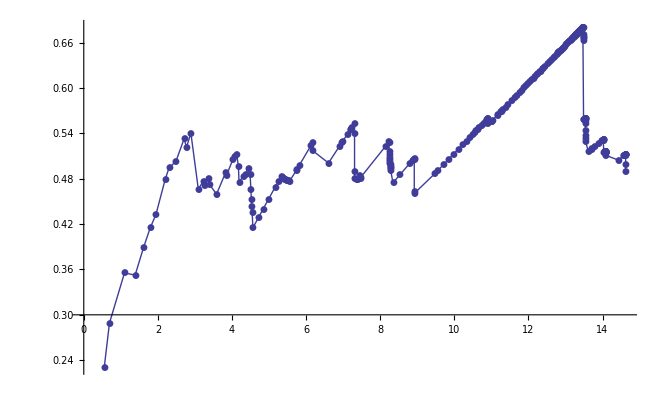

```mathematica
ListPlot[Map[{Log[#[[1]]],Log[#[[1]]]/Log[#[[2]]]}&,l],  Joined->True, PlotMarkers->Automatic]
```